```mathematica
latticePointListSC[δ_]:= With[{n = Ceiling[δ]},
Select[DeleteCases[Flatten[Table[{i,j,k},
{i,-n,n},{j,-n,n},{k,-n,n}],2], (* without origin *) {0,0,0}], #. #≤ δ^2&]]
```

```mathematica
maxDist = 4;
Length[latticePoints = latticePointListSC[maxDist]]
```

256

```mathematica
Show[Graphics3D[Cuboid[# + 0.1 {1,1,1},
# - 0.1 {1,1,1}]& /@ latticePoints],Axes->True]
```

-Graphics3D-

```mathematica
(* a function for normalizing vector *)
𝓃 = #/Sqrt[#.#]&;
```

```mathematica
toPlane[p:latticePoint_]:=
Plane[latticePoint/2,
Which[(* lattice point is on coordinate axis *)
p[[1]] == 0 && p[[2]]==0, {{1,0,0},{0,1,0}},
p[[1]] == 0 && p[[3]]==0, {{1,0,0},{0,0,1}},
p[[2]] == 0 && p[[3]]==0,  {{0,1,0},{0,0,1}},
(* lattice point is on a coordinate plane *)
p[[1]] ≠ 0 && p[[2]] ≠ 0, {#,Cross[#,p]}&[{p[[2]],-p[[1]],0}],
p[[1]] ≠0  && p[[3]] ≠ 0, {#,Cross[#,p]}&[{p[[3]],0,-p[[1]]}],
p[[2]] ≠0  && p[[3]] ≠ 0, {#,Cross[#,p]}&[{0,p[[3]],-p[[2]]}],
(* lattice point is in generic position *)
True, {#,Cross[#,p]}&[{p[[2]],-p[[1]],0}]]]
```

```mathematica
symmetrySlicingPlanes =
Plane[{0,0,0}, #]& /@
{{{1,0,0},{0,1,0}},{{1,0,0},{0,0,1}},
{{0,1,0},{0,0,1}},{{0,0,1},{-1,1,0}},
{{0,0,1},{1,1,0}},{{1,0,0},{0,-1,1}},
{{1,0,0},{0,1,1}},{{0,1,0},{-1,0,1}},
{{0,1,0},{1,0,1}}};
```

```mathematica
With[{ϵ=0.05},
Show[Graphics3D[{(*make polygons*)
Polygon[{#[[1]]-#[[2,1]]-#[[2,2]],#[[1]]+#[[2,1]]-#[[2,2]],
#[[1]] + #[[2,1]] + #[[2,2]], #[[1]] - #[[2,1]]+#[[2,2]]}]& /@ symmetrySlicingPlanes,
{SurfaceColor[Hue[0]], (* lift up a bit *)
Map[# + {ϵ,ϵ,2ϵ}&, (* boundary of the unit cone *)
{Polygon[{{0,0,0},{0,0,1},{1,0,1}}],
Polygon[{{0,0,0},{0,0,1},{1,1,1}}],
Polygon[{{0,0,0},{1,0,1},{1,1,1}}]},
{-2}]}}],Boxed->False]]
```

-Graphics3D-

```mathematica
planes = Join[toPlane /@ latticePoints, symmetrySlicingPlanes];
```

```mathematica
Take[planes,4]
```

{Plane[{-2,0,0},{{0,1,0},{0,0,1}}],Plane[{-3/2,-1,-1/2},{{-2,3,0},{-3,-2,13}}],Plane[{-3/2,-1,0},{{-2,3,0},{0,0,13}}],Plane[{-3/2,-1,1/2},{{-2,3,0},{3,2,13}}]}

```mathematica
(* three equations cannot be solved for four variables *)
Off[Solve::"svars"];

lineOnPlane[Plane[p_,{dir1_,dir2_}],Plane[q_, {d1_,d2_}]]:=
 Module[{eqs, sol, line, var, aux, P1,P2},
If[(* are the planes parallel? *)
Length[DeleteCases[
RowReduce[{dir1,dir2,d1,d2}],{0,0,0},{1}]] ==2,{},
(* calculate direction of the intersecting line *)
eqs = Thread[p+ s dir1 + t dir2 == q + u d1 + v d2];
sol = Solve[eqs, {u,v,s,t}];

aux = p + s dir1 + t dir2 /. sol[[1]];
(* two points on the line *)
{P1,P2} = {aux /. {u->0,v->0},aux /. {u->1,v->1}};
Line[P1,P2-P1]]]
planes[[5]]
```

Plane[{-3/2,-1/2,-1},{{-1,3,0},{-6,-2,10}}]

```mathematica
lineOnPlane[planes[[1]],planes[[5]]]
```

{-2,-2/3+(10 u)/3,-1/6-(5 u)/3}

Line[{-2,-2/3,-1/6},{0,10/3,-5/3}]

```mathematica
lineOnPlane[planes[[1]],planes[[11]]]
```

{-2,-10 v,1}

Line[{-2,0,1},{0,-10,0}]

```mathematica
(linesOnPlane1 = DeleteCases[Table[lineOnPlane[planes[[1]],planes[[i]]],
{i,2,Length[planes]}],{},{1}];)//Timing
```

{-2,-4/3+(13 u)/3,5/3-(26 u)/3}

{-2,-1/4,13 v}

{-2,-4/3+(13 u)/3,-5/3+(26 u)/3}

{-2,-2/3+(10 u)/3,-1/6-(5 u)/3}

{-2,-2/3+(10 u)/3,7/6-(10 u)/3}

{-2,1,10 v}

{-2,-2/3+(10 u)/3,-7/6+(10 u)/3}

{-2,-2/3+(10 u)/3,1/6+(5 u)/3}

{-2,-13 v,-1/4}

{-2,-10 v,1}

{-2,-10 v,-1}

{-2,-13 v,1/4}

{-2,2/3+(10 u)/3,-1/6+(5 u)/3}

{-2,2/3+(10 u)/3,7/6+(10 u)/3}

{-2,-1,10 v}

{-2,2/3+(10 u)/3,-7/6-(10 u)/3}

{-2,2/3+(10 u)/3,1/6-(5 u)/3}

{-2,4/3+(13 u)/3,5/3+(26 u)/3}

{-2,1/4,13 v}

{-2,4/3+(13 u)/3,-5/3-(26 u)/3}

{-2,-3+(13 u)/2,6-(39 u)/2}

{-2,-5/6,13 v}

{-2,-3+(13 u)/2,-6+(39 u)/2}

{-2,-2+4 u,1-4 u}

{-2,-2+4 u,7/2-8 u}

{-2,0,8 v}

{-2,-2+4 u,-7/2+8 u}

{-2,-2+4 u,-1+4 u}

{-2,-1+(5 u)/2,-2/3-(5 u)/6}

{-2,-1+(5 u)/2,1/4-(5 u)/4}

{-2,-1+(5 u)/2,2-(5 u)/2}

{-2,3/2,5 v}

{-2,-1+(5 u)/2,-2+(5 u)/2}

{-2,-1+(5 u)/2,-1/4+(5 u)/4}

{-2,-1+(5 u)/2,2/3+(5 u)/6}

{-2,-13 v,-5/6}

{-2,-8 v,0}

{-2,-5 v,3/2}

{-2,-5 v,-3/2}

{-2,-8 v,0}

{-2,-13 v,5/6}

{-2,1+(5 u)/2,-2/3+(5 u)/6}

{-2,1+(5 u)/2,1/4+(5 u)/4}

{-2,1+(5 u)/2,2+(5 u)/2}

{-2,-3/2,5 v}

{-2,1+(5 u)/2,-2-(5 u)/2}

{-2,1+(5 u)/2,-1/4-(5 u)/4}

{-2,1+(5 u)/2,2/3-(5 u)/6}

{-2,2+4 u,1+4 u}

{-2,2+4 u,7/2+8 u}

{-2,0,8 v}

{-2,2+4 u,-7/2-8 u}

{-2,2+4 u,-1-4 u}

{-2,3+(13 u)/2,6+(39 u)/2}

{-2,5/6,13 v}

{-2,3+(13 u)/2,-6-(39 u)/2}

{-2,-6+10 u,13/2-15 u}

{-2,-6+10 u,29/2-30 u}

{-2,-1,10 v}

{-2,-6+10 u,-29/2+30 u}

{-2,-6+10 u,-13/2+15 u}

{-2,-4+5 u,1-(10 u)/3}

{-2,-4+5 u,11/4-5 u}

{-2,-4+5 u,7-10 u}

{-2,-1/4,5 v}

{-2,-4+5 u,-7+10 u}

{-2,-4+5 u,-11/4+5 u}

{-2,-4+5 u,-1+(10 u)/3}

{-2,-2+2 u,-1/2-(2 u)/3}

{-2,-2+2 u,1/2-u}

{-2,-2+2 u,5/2-2 u}

{-2,1,2 v}

{-2,-2+2 u,-5/2+2 u}

{-2,-2+2 u,-1/2+u}

{-2,-2+2 u,1/2+(2 u)/3}

{-2,-10 v,-1}

{-2,-5 v,-1/4}

{-2,-2 v,1}

{-2,-2 v,-1}

{-2,-5 v,1/4}

{-2,-10 v,1}

{-2,2+2 u,-1/2+(2 u)/3}

{-2,2+2 u,1/2+u}

{-2,2+2 u,5/2+2 u}

{-2,-1,2 v}

{-2,2+2 u,-5/2-2 u}

{-2,2+2 u,-1/2-u}

{-2,2+2 u,1/2-(2 u)/3}

{-2,4+5 u,1+(10 u)/3}

{-2,4+5 u,11/4+5 u}

{-2,4+5 u,7+10 u}

{-2,1/4,5 v}

{-2,4+5 u,-7-10 u}

{-2,4+5 u,-11/4-5 u}

{-2,4+5 u,-1-(10 u)/3}

{-2,6+10 u,13/2+15 u}

{-2,6+10 u,29/2+30 u}

{-2,1,10 v}

{-2,6+10 u,-29/2-30 u}

{-2,6+10 u,-13/2-15 u}

{-2,-2,v}

{-2,-3/2-2 u,-1+3 u}

{-2,-3/2-u,-1/2+3 u}

{-2,-3/2,v}

{-2,-3/2+u,1/2+3 u}

{-2,-3/2+2 u,1+3 u}

{-2,-1-3 u,-3/2+2 u}

{-2,-1-2 u,-1+2 u}

{-2,-1-u,-1/2+2 u}

{-2,-1,v}

{-2,-1+u,1/2+2 u}

{-2,-1+2 u,1+2 u}

{-2,-1+3 u,3/2+2 u}

{-2,-1/2-3 u,-3/2+u}

{-2,-1/2-2 u,-1+u}

{-2,-1/2-u,-1/2+u}

{-2,-1/2,v}

{-2,-1/2+u,1/2+u}

{-2,-1/2+2 u,1+u}

{-2,-1/2+3 u,3/2+u}

{-2,v,-2}

{-2,v,-3/2}

{-2,v,-1}

{-2,v,-1/2}

{-2,v,1/2}

{-2,v,1}

{-2,v,3/2}

{-2,v,2}

{-2,1/2-3 u,-3/2-u}

{-2,1/2-2 u,-1-u}

{-2,1/2-u,-1/2-u}

{-2,1/2,v}

{-2,1/2+u,1/2-u}

{-2,1/2+2 u,1-u}

{-2,1/2+3 u,3/2-u}

{-2,1-3 u,-3/2-2 u}

{-2,1-2 u,-1-2 u}

{-2,1-u,-1/2-2 u}

{-2,1,v}

{-2,1+u,1/2-2 u}

{-2,1+2 u,1-2 u}

{-2,1+3 u,3/2-2 u}

{-2,3/2-2 u,-1-3 u}

{-2,3/2-u,-1/2-3 u}

{-2,3/2,v}

{-2,3/2+u,1/2-3 u}

{-2,3/2+2 u,1-3 u}

{-2,2,v}

{-2,6-10 u,-27/2+15 u}

{-2,6-10 u,-51/2+30 u}

{-2,-7/3,10 v}

{-2,6-10 u,51/2-30 u}

{-2,6-10 u,27/2-15 u}

{-2,4-5 u,-17/3+(10 u)/3}

{-2,4-5 u,-29/4+5 u}

{-2,4-5 u,-13+10 u}

{-2,-9/4,5 v}

{-2,4-5 u,13-10 u}

{-2,4-5 u,29/4-5 u}

{-2,4-5 u,17/3-(10 u)/3}

{-2,2-2 u,-19/6+(2 u)/3}

{-2,2-2 u,-7/2+u}

{-2,2-2 u,-11/2+2 u}

{-2,-3,2 v}

{-2,2-2 u,11/2-2 u}

{-2,2-2 u,7/2-u}

{-2,2-2 u,19/6-(2 u)/3}

{-2,-10 v,-7/3}

{-2,-5 v,-9/4}

{-2,-2 v,-3}

{-2,-2 v,3}

{-2,-5 v,9/4}

{-2,-10 v,7/3}

{-2,-2-2 u,-19/6-(2 u)/3}

{-2,-2-2 u,-7/2-u}

{-2,-2-2 u,-11/2-2 u}

{-2,3,2 v}

{-2,-2-2 u,11/2+2 u}

{-2,-2-2 u,7/2+u}

{-2,-2-2 u,19/6+(2 u)/3}

{-2,-4-5 u,-17/3-(10 u)/3}

{-2,-4-5 u,-29/4-5 u}

{-2,-4-5 u,-13-10 u}

{-2,9/4,5 v}

{-2,-4-5 u,13+10 u}

{-2,-4-5 u,29/4+5 u}

{-2,-4-5 u,17/3+(10 u)/3}

{-2,-6-10 u,-27/2-15 u}

{-2,-6-10 u,-51/2-30 u}

{-2,7/3,10 v}

{-2,-6-10 u,51/2+30 u}

{-2,-6-10 u,27/2+15 u}

{-2,3-(13 u)/2,-20+(39 u)/2}

{-2,-7/2,13 v}

{-2,3-(13 u)/2,20-(39 u)/2}

{-2,2-4 u,-7+4 u}

{-2,2-4 u,-25/2+8 u}

{-2,-4,8 v}

{-2,2-4 u,25/2-8 u}

{-2,2-4 u,7-4 u}

{-2,1-(5 u)/2,-4+(5 u)/6}

{-2,1-(5 u)/2,-19/4+(5 u)/4}

{-2,1-(5 u)/2,-8+(5 u)/2}

{-2,-13/2,5 v}

{-2,1-(5 u)/2,8-(5 u)/2}

{-2,1-(5 u)/2,19/4-(5 u)/4}

{-2,1-(5 u)/2,4-(5 u)/6}

{-2,-13 v,-7/2}

{-2,-8 v,-4}

{-2,-5 v,-13/2}

{-2,-5 v,13/2}

{-2,-8 v,4}

{-2,-13 v,7/2}

{-2,-1-(5 u)/2,-4-(5 u)/6}

{-2,-1-(5 u)/2,-19/4-(5 u)/4}

{-2,-1-(5 u)/2,-8-(5 u)/2}

{-2,13/2,5 v}

{-2,-1-(5 u)/2,8+(5 u)/2}

{-2,-1-(5 u)/2,19/4+(5 u)/4}

{-2,-1-(5 u)/2,4+(5 u)/6}

{-2,-2-4 u,-7-4 u}

{-2,-2-4 u,-25/2-8 u}

{-2,4,8 v}

{-2,-2-4 u,25/2+8 u}

{-2,-2-4 u,7+4 u}

{-2,-3-(13 u)/2,-20-(39 u)/2}

{-2,7/2,13 v}

{-2,-3-(13 u)/2,20+(39 u)/2}

{-2,4/3-(13 u)/3,-47/3+(26 u)/3}

{-2,-25/4,13 v}

{-2,4/3-(13 u)/3,47/3-(26 u)/3}

{-2,2/3-(10 u)/3,-41/6+(5 u)/3}

{-2,2/3-(10 u)/3,-73/6+(10 u)/3}

{-2,-11,10 v}

{-2,2/3-(10 u)/3,73/6-(10 u)/3}

{-2,2/3-(10 u)/3,41/6-(5 u)/3}

{-2,-13 v,-25/4}

{-2,-10 v,-11}

{-2,-10 v,11}

{-2,-13 v,25/4}

{-2,-2/3-(10 u)/3,-41/6-(5 u)/3}

{-2,-2/3-(10 u)/3,-73/6-(10 u)/3}

{-2,11,10 v}

{-2,-2/3-(10 u)/3,73/6+(10 u)/3}

{-2,-2/3-(10 u)/3,41/6+(5 u)/3}

{-2,-4/3-(13 u)/3,-47/3-(26 u)/3}

{-2,25/4,13 v}

{-2,-4/3-(13 u)/3,47/3+(26 u)/3}

{-2,v,0}

{-2,0,v}

{-2,2,u}

{-2,-2,u}

{-2,-v,v}

{-2,v,v}

{-2,u,2}

{-2,u,-2}

{0.109375,Null}

```mathematica
Length[linesOnPlane1]
```

256

```mathematica
Take[linesOnPlane1,3]
```

{Line[{-2,-4/3,5/3},{0,13/3,-26/3}],Line[{-2,-1/4,0},{0,0,13}],Line[{-2,-4/3,-5/3},{0,13/3,26/3}]}

```mathematica
lineDistanceSquare[Line[p_,dir_]] := #.#&[p-dir.p/dir.dir  dir]
```

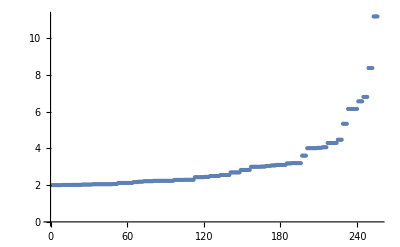

```mathematica
ListPlot[Sqrt[Sort[N[lineDistanceSquare /@ linesOnPlane1]]],
PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
linesOnPlane1 = Select[linesOnPlane1, lineDistanceSquare[#] < maxDist^2&];
```

```mathematica
Length[linesOnPlane1]
```

200

```mathematica
Off[LinearSolve::nosol];
lineIntersection[Line[p1_,dir1_],Line[p2_,dir2_],δ_]:=Module[{ls},
(* are the two line the same? *)
If[(Length[DeleteCases[RowReduce[{dir1,dir2}],
{0,0,0},{1}]]===1) &&
(* check head *)
Head[LinearSolve[Transpose[{dir1}],
p2 - p1]] =!= LinerSolve,Sequence @@ {},
(* the actual intersection (if any) *)
ls = LinearSolve[Transpose[{dir1,dir1}],p2-p1];
If[Head[ls] === LinearSolve, Sequence @@ {},
(* inside the sphere of interest ? *)
If[#.# < δ^2, Point @ #, Sequence @@ {} ] & [
p1 +ls[[1]] dir1]]]]
```

```mathematica
intersectionsPlanes1=DeleteCases[Table[If[i == j, Sequence @@ {},
lineIntersection[linesOnPlane1[[j]],linesOnPlane1[[i]],3/4 maxDist]],
{j,Length[linesOnPlane1]},{i,Length[linesOnPlane1]}],
{},{1}]; //Timing
```

{1.90625,Null}

```mathematica
Length[Flatten[intersectionsPlanes1]]
```

864

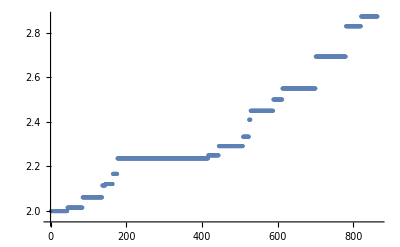

```mathematica
ListPlot[Sort[Sqrt[#[[1]].#[[1]]]& /@ N[Flatten[intersectionsPlanes1]]],PlotRange->All]
```

```mathematica
lineSegments[points_]:= Module[{points1 = Union[First /@ points],
distancesFromOrigin, startPoint},
(* distances from chosen point *)
distancesFromOrigin = #.# & /@ points1;
(* furthest point *)
startPoint = points1[[ Position[distancesFromOrigin,
Max[distancesFromOrigin]][[1,1]] ]];
(* sort points according to distance and form pairs *)
Line /@ Partition[Sort [points1,
(#.#&[#1 -startPoint] < 
#.#&[#2 - startPoint] )&],2,1]]
```

```mathematica
lineSegmentsPlane1 = lineSegments /@ intersectionsPlanes1;
```

```mathematica
Length[Flatten[lineSegmentsPlane1]]
```

452

```mathematica
contract[Line[{p1_,p2_}], f_] :=
Module[{mp = (p1 + p2)}, Line[{mp + f (p1-mp),mp + f(p2-mp)}]]
```

```mathematica
Show[Graphics3D[{Hue[Random[]],
contract[#,0.8]& /@ #}& /@ lineSegmentsPlane1],
BoxRatios->{1, 1, 1},Axes->True,
(* view perpendicular *) ViewPoint->4 latticePoints[[1]]]
```

-Graphics3D-

```mathematica
makeSpindle[Line[{p1_,p2_}]]:=
Module[{dir1, dir2, dir3, aux, mp = (p1 + p2)/2,
l = Sqrt[(p2-p1).(p2-p1)], n = 6},
(* three orthogonal directions *)
dir1  = 𝓃[p2-p1];
dir2  = 𝓃[Table[Random[],{3}]];
dir2 = 𝓃[dir2-dir1.dir2 dir1];
dir3 = Cross[dir1,dir2];
(* the spindle *)
aux = Table[mp + 1/12 (Cos[φ] dir2 + Sin[φ] dir3),
{φ, 0, 2. Pi, 2.Pi/n}];
{Polygon[Append[#,p1]],Polygon[Append[#,p2]]}& /@
Partition[aux,2,1]]
```

```mathematica
Show[Graphics3D[{EdgeForm[],{SurfaceColor[Hue[Random[]]],
makeSpindle[#]}& /@ Flatten[lineSegmentsPlane1]}],
BoxRatios->{1, 1, 1},ViewPoint->{3,0,1},
PlotRange->2.1{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
{#[[1]],Length[#]}& /@ Split[Sort[Length /@ Split[Sort[Join[#, Reverse /@ #]& [First /@ Flatten[lineSegmentsPlane1]]],#1[[1]] === #2[[1]]&]]]
```

{{2,4},{4,4},{5,4},{6,8},{7,4},{8,4},{10,20},{14,4},{15,8},{16,5},{22,4},{24,2},{26,4},{28,2}}

```mathematica
allLineSegmentsPlane1=Join[#,Map[Reverse, #,{2}]]& [Flatten[(*give name*) directedLineSegmentsPlane1 = Union[Ma
```